## Function Definitions

Don’t forget that there’s also an omega floating around

### For m = 0

```mathematica
const1=1/(2*Pi)
```

1/(2 π)

```mathematica
p0[e_,s_]:=const1*Integrate[Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi},Assumptions->{e≥0,e≤1,Element[s,Integers]}]
```

```mathematica
Np0[e_,s_]:=const1*NIntegrate[Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi}]
```

```mathematica
p0NoPole[e_,s_]:=const1*Integrate[(1-e^2)^(3/2)*Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi},Assumptions->{e≥0,e≤1,Element[s,Integers]}]
```

```mathematica
Np0NoPole[e_,s_]:=const1*NIntegrate[(1-e^2)^(3/2)*Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^2,{u,0,2*Pi}]
```

### For m = 2

There’s also an Exp[phi_not]

```mathematica
const2=Exp[I*2]
```

ⅇ^(2 ⅈ)

#### Sub integrals

```mathematica
pTwoA[e_,s_]:=const1*(1-e^2)*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4),{u,0,2*Pi},Assumptions->{e≥0,e≤1}]
```

```mathematica
pTwoB[e_,s_]:=const1*(1-e^2)*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Cos[2*u],{u,0,2*Pi},Assumptions->{e≥0,e≤1}]
```

```mathematica
pTwoC[e_,s_]:=const1*I*Sqrt[(1-e^2)]*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[2*u],{u,0,2*Pi},Assumptions->{e≥0,e≤1}]
```

```mathematica
pTwoD[e_,s_]:=const1*I*2*e*Sqrt[(1-e^2)]*Integrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[u],{u,0,2*Pi},Assumptions->{e≥0,e≤1}]
```

#### Main Coefficients

```mathematica
pPlus2[e_,s_]:=(1/(const1*const2))*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]-pTwoC[e,s]+pTwoD[e,s])
```

```mathematica
pMinus2[e_,s_]:=(const2/const1)*(p0[e,s]-pTwoA[e,s]+pTwoB[e,s]+pTwoC[e,s]-pTwoD[e,s])
```

#### Also numerical integration versions

```mathematica
NpTwoA[e_,s_]:=const1*(1-e^2)*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4),{u,0,2*Pi}]
```

```mathematica
NpTwoB[e_,s_]:=const1*(1-e^2)*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Cos[2*u],{u,0,2*Pi}]
```

```mathematica
NpTwoC[e_,s_]:=const1*I*Sqrt[(1-e^2)]*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[2*u],{u,0,2*Pi}]
```

```mathematica
NpTwoD[e_,s_]:=const1*I*2*e*Sqrt[(1-e^2)]*NIntegrate[(Exp[I*s*(u-e*Sin[u])] / (1-e*Cos[u])^4)*Sin[u],{u,0,2*Pi}]
```

```mathematica
NpPlus2[e_,s_]:=(1/(const1*const2))*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

```mathematica
NpMinus2[e_,s_]:=(const2/const1)*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]+NpTwoC[e,s]-NpTwoD[e,s])
```

```mathematica
NpPlus2NP[e_,s_]:=((1-e^2)^(3/2)/(const1*const2))*(Np0[e,s]-NpTwoA[e,s]+NpTwoB[e,s]-NpTwoC[e,s]+NpTwoD[e,s])
```

## Verifying Values

```mathematica
p0[e,0]
```

ConditionalExpression[1/((1-e^2)^(3/2)),0<e<1]

```mathematica
p0NoPole[e,0]
```

ConditionalExpression[1,0<e<1]

```mathematica
pPlus2[e,0]
```

ConditionalExpression[2 ((5 e^2)/(2 (1-e^2)^(5/2))+1/((1-e^2)^(3/2))-(2+3 e^2)/(2 (1-e^2)^(5/2))) ⅇ^(-2 ⅈ) π,0<e<1]

```mathematica
FullSimplify[ConditionalExpression[2 ((5 e^2)/(2 (1-e^2)^(5/2))+1/((1-e^2)^(3/2))-(2+3 e^2)/(2 (1-e^2)^(5/2))) ⅇ^(-2 ⅈ) π,0<e<1]]
```

ConditionalExpression[0,0<e<1]

```mathematica
FullSimplify[pMinus2[e,0]]
```

ConditionalExpression[0,0<e<1]

## Now I’m Messing Around with Things

```mathematica
p0[e,1]
```

$Aborted

```mathematica
Np0NoPole[e,0]
```

NIntegrate::inumr: The integrand (1 - e^2)^3/2/(1 - e\ Cos[u])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

NIntegrate[((1-e^2)^(3/2) Exp[ⅈ 0 (u-e Sin[u])])/(1-e Cos[u])^2,{u,0,2 π}]/(2 π)

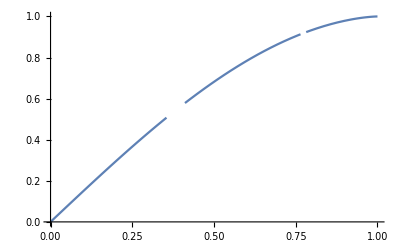

```mathematica
Plot[Np0NoPole[e,1],{e,0,1}]
```

```mathematica
p0NoPole[e,1]
```

$Aborted

```mathematica
Series
```

```mathematica
With[{e=.9},NpPlus2[e,1]]
```

1.10677+2.41834 ⅈ

```mathematica
Im[With[{e=.9},NpPlus2[e,1]]]/Re[With[{e=.9},NpPlus2[e,1]]]
```

2.18504

```mathematica
With[{e=.5},NpPlus2[e,1]]
```

0.634516+1.38644 ⅈ

```mathematica
Im[With[{e=.5},NpPlus2[e,1]]]/Re[With[{e=.5},NpPlus2[e,1]]]
```

2.18504

```mathematica
With[{e=.1},NpPlus2[e,1]]
```

0.130573+0.285308 ⅈ

```mathematica
Im[With[{e=.1},NpPlus2[e,1]]]/Re[With[{e=.1},NpPlus2[e,1]]]
```

2.18504

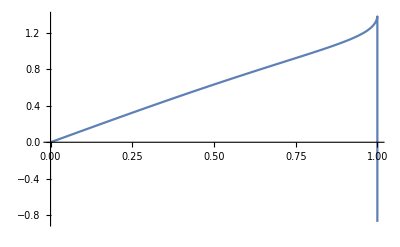

```mathematica
Plot[Re[NpPlus2[e,1]],{e,0,1}]
```

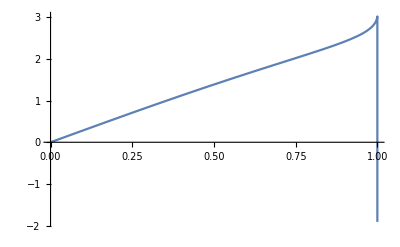

```mathematica
Plot[Im[NpPlus2[e,1]],{e,0,1}]
```

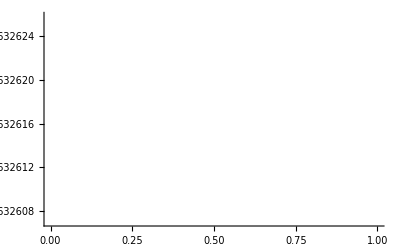

```mathematica
Plot[Im[NpPlus2[e,1]]/Re[NpPlus2[e,1]],{e,0,1}]
```

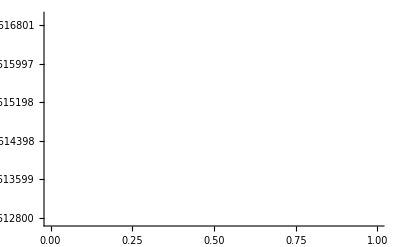

```mathematica
Plot[Im[NpPlus2[e,2]]/Re[NpPlus2[e,2]],{e,0,1}]
```

```mathematica
With[{e=.9},NpPlus2[e,2]]
```

1.50553+3.28964 ⅈ

```mathematica
Im[With[{e=.9},NpPlus2[e,2]]]/Re[With[{e=.9},NpPlus2[e,2]]]
```

2.18504

```mathematica
With[{e=.5},NpPlus2[e,2]]
```

-1.1082-2.42147 ⅈ

```mathematica
Im[With[{e=.5},NpPlus2[e,2]]]/Re[With[{e=.5},NpPlus2[e,2]]]
```

2.18504

```mathematica
With[{e=.1},NpPlus2[e,2]]
```

-2.54957-5.57092 ⅈ

```mathematica
Im[With[{e=.1},NpPlus2[e,2]]]/Re[With[{e=.1},NpPlus2[e,2]]]
```

2.18504

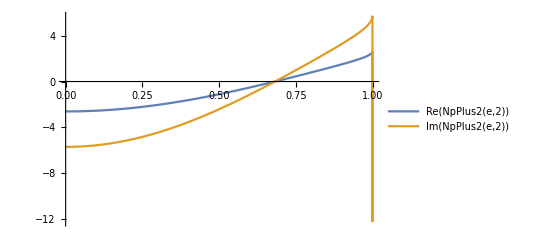

```mathematica
Plot[{Re[NpPlus2[e,2]],Im[NpPlus2[e,2]]},{e,0,1},PlotLegends->"Expressions"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

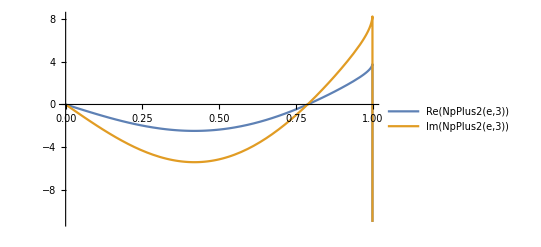

```mathematica
Plot[{Re[NpPlus2[e,3]],Im[NpPlus2[e,3]]},{e,0,1},PlotLegends->"Expressions"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained -6.59195×10^-16 + 4.16334×10^-16\ ⅈ and 1.50742×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained -7.63278×10^-16 - 2.43729×10^-16\ ⅈ and 1.09633×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained 3.1225×10^-17 + 3.4366×10^-13\ ⅈ and 8.65141×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

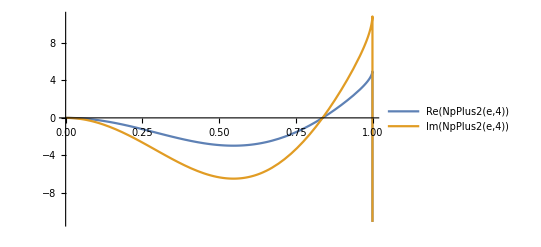

```mathematica
Plot[{Re[NpPlus2[e,4]],Im[NpPlus2[e,4]]},{e,0,1},PlotLegends->"Expressions"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained -6.59195×10^-16 + 4.16334×10^-16\ ⅈ and 1.50742×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained -7.63278×10^-16 - 2.43729×10^-16\ ⅈ and 1.09633×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained 3.1225×10^-17 + 3.4366×10^-13\ ⅈ and 8.65141×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

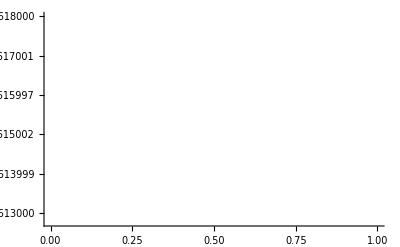

```mathematica
Plot[Im[NpPlus2[e,4]]/Re[NpPlus2[e,4]],{e,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831852508345497179263397537840672279346732054250423971097916365}. NIntegrate obtained -6.22766×10^-16 + 1.38778×10^-17\ ⅈ and 8.45301×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.0558}. NIntegrate obtained -8.22259×10^-16 - 2.61076×10^-16\ ⅈ and 2.71231×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831852508345497179263397537840672279346732054250423971097916365}. NIntegrate obtained -4.67508×10^-16 - 6.245×10^-17\ ⅈ and 8.54053×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

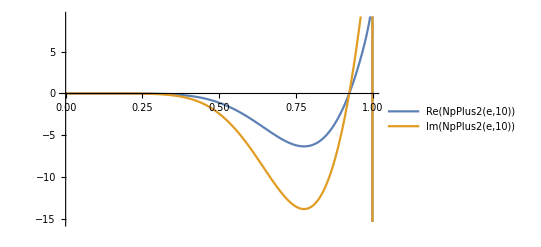

```mathematica
Plot[{Re[NpPlus2[e,10]],Im[NpPlus2[e,10]]},{e,0,1},PlotLegends->"Expressions"]
```

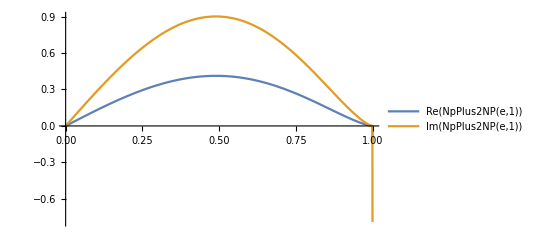

```mathematica
Plot[{Re[NpPlus2NP[e,1]],Im[NpPlus2NP[e,1]]},{e,0,1},PlotLegends->"Expressions"]
```

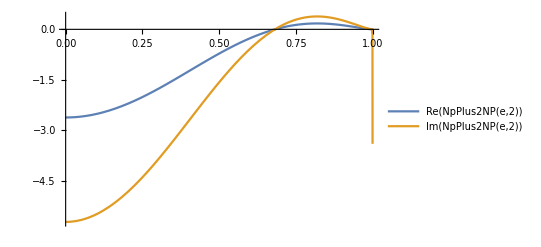

```mathematica
Plot[{Re[NpPlus2NP[e,2]],Im[NpPlus2NP[e,2]]},{e,0,1},PlotLegends->"Expressions"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {5.32588}. NIntegrate obtained 4.84522×10^-13 + 2.18575×10^-16\ ⅈ and 1.04604×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76956×10^-13 + 4.16334×10^-17\ ⅈ and 1.36788×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

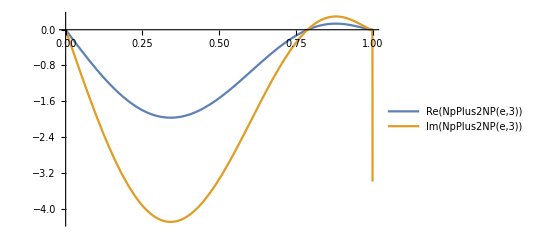

```mathematica
Plot[{Re[NpPlus2NP[e,3]],Im[NpPlus2NP[e,3]]},{e,0,1},PlotLegends->"Expressions"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {1.1269×10^-7}. NIntegrate obtained -6.59195×10^-16 + 4.16334×10^-16\ ⅈ and 1.50742×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained -7.63278×10^-16 - 2.43729×10^-16\ ⅈ and 1.09633×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.70002}. NIntegrate obtained 3.1225×10^-17 + 3.4366×10^-13\ ⅈ and 8.65141×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

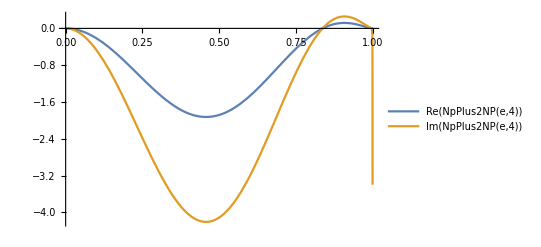

```mathematica
Plot[{Re[NpPlus2NP[e,4]],Im[NpPlus2NP[e,4]]},{e,0,1},PlotLegends->"Expressions"]
```

```mathematica
With[{e=.999},NpPlus2NP[e,2]]
```

0.000228858+0.000500064 ⅈ

```mathematica
Series[pPlus2[e,1],{e,0,2}]
```

$Aborted